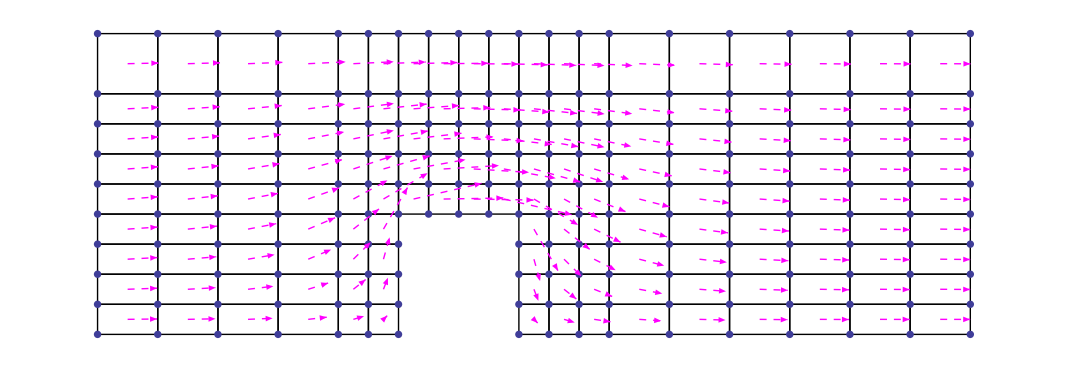

```mathematica
Nodelist=Import["Desktop/ChnlNodes.Dat"];
Elementlist=Import["Desktop/ChnlElems.Dat"];

nodes={};
elements={};
elementpointer={};
elementlines={};

K=ConstantArray[0,{Length[Nodelist],Length[Nodelist]}];

For[i=1,i≤ Length[Nodelist],i++,
AppendTo[nodes,{Nodelist[[i]][[2]], Nodelist[[i]][[3]]}
];
];

For[p=1,p≤ Length[Elementlist],p++,
AppendTo[elementpointer,
{
Elementlist[[p]][[2]],
Elementlist[[p]][[3]],
Elementlist[[p]][[4]],
Elementlist[[p]][[5]]
}
];
];

For[h =1,h≤ Length[Elementlist],h++,

AppendTo[elementlines,
Line[
{
nodes[[Elementlist[[h]][[2]]]],
nodes[[Elementlist[[h]][[3]]]],
nodes[[Elementlist[[h]][[4]]]],
nodes[[Elementlist[[h]][[5]]]],
nodes[[Elementlist[[h]][[2]]]]
}
]]];

For[k=1,k≤ Length[Elementlist],k++,
AppendTo[elements,
{
nodes[[elementpointer[[k]][[1]]]],
nodes[[elementpointer[[k]][[2]]]],
nodes[[elementpointer[[k]][[3]]]],
nodes[[elementpointer[[k]][[4]]]]
}
]
];

Subscript[N, 1][α_,β_,γ_,δ_,x_,y_]:=(γ-x)/(γ-α)*(δ-y)/(δ-β) ;
Subscript[N, 2][α_,β_,γ_,δ_,x_,y_]:=(x-α)/(γ-α)*(δ-y)/(δ-β) ;
Subscript[N, 3][α_,β_,γ_,δ_,x_,y_]:=(x-α)/(γ-α)*(y-β)/(δ-β) ;
Subscript[N, 4][α_,β_,γ_,δ_,x_,y_]:=(γ-x)/(γ-α)*(y-β)/(δ-β) ;

Polyfuction={Subscript[N, 1],Subscript[N, 2],Subscript[N, 3],Subscript[N, 4]};

For[m=1,m≤Length[elements],m++,
For[n=1,n≤ Length[Polyfuction],n++,
For[o=1,o≤ Length[Polyfuction],o++,

elementcounter=elementpointer[[m]];
columns=elementcounter[[o]];
rows=elementcounter[[n]];

α=nodes[[elementcounter[[1]]]][[1]];
β=nodes[[elementcounter[[1]]]][[2]];
γ=nodes[[elementcounter[[3]]]][[1]];
δ=nodes[[elementcounter[[3]]]][[2]];

Subscript[g, n]=Grad[Subscript[N, n][α,β,γ,δ,x,y],{x,y}];
Subscript[g, o]=Grad[Subscript[N, o][α,β,γ,δ,x,y],{x,y}];

K[[rows,columns]]=K[[rows,columns]]+NIntegrate[Dot[Subscript[g, o],Subscript[g, n]],{x,α,γ},{y,β,δ}];

];
];
];

R=ConstantArray[0,Length[Nodelist]];

For[t=1,t≤9,t++,

elementcounter=elementpointer[[t]];

α=nodes[[elementcounter[[1]]]][[1]];
β=nodes[[elementcounter[[1]]]][[2]];
γ=nodes[[elementcounter[[3]]]][[1]];
δ=nodes[[elementcounter[[3]]]][[2]];

R[[elementcounter[[1]]]]=R[[elementcounter[[1]]]]+NIntegrate[-Subscript[N, 1][α,β,γ,δ,α,y],{y,β,δ}];
R[[elementcounter[[4]]]]=R[[elementcounter[[4]]]]+NIntegrate[-Subscript[N, 4][α,β,γ,δ,α,y],{y,β,δ}];

]

For[u=Length[elements]-8,u≤ Length[elements],u++,

elementcounter=elementpointer[[u]];

α=nodes[[elementcounter[[1]]]][[1]];
β=nodes[[elementcounter[[1]]]][[2]];
γ=nodes[[elementcounter[[3]]]][[1]];
δ=nodes[[elementcounter[[3]]]][[2]];

R[[elementcounter[[2]]]]=R[[elementcounter[[2]]]]+NIntegrate[Subscript[N, 2][α,β,γ,δ,γ,y],{y,β,δ}];
R[[elementcounter[[3]]]]=R[[elementcounter[[3]]]]+NIntegrate[Subscript[N, 3][α,β,γ,δ,γ,y],{y,β,δ}];

];

bound=ConstantArray[0,Length[R]];
bound[[61]]=1;
K[[61]]=bound;
R[[61]]=0;

alpha=LinearSolve[K,R];
arrows=ConstantArray[0,Length[elements]];
half=0.5;

For[v=1,v≤ Length[elements], v++,

elementcounter=elementpointer[[v]];

α=nodes[[elementcounter[[1]]]][[1]];
β=nodes[[elementcounter[[1]]]][[2]];
γ=nodes[[elementcounter[[3]]]][[1]];
δ=nodes[[elementcounter[[3]]]][[2]];

centerx=(α+γ)/2;
centery=(β+δ)/2;

potential[x_,y_]:=alpha[[elementcounter[[1]]]]*Subscript[N, 1][α,β,γ,δ,x,y]+alpha[[elementcounter[[2]]]]*Subscript[N, 2][α,β,γ,δ,x,y]+alpha[[elementcounter[[3]]]]*Subscript[N, 3][α,β,γ,δ,x,y]+alpha[[elementcounter[[4]]]]*Subscript[N, 4][α,β,γ,δ,x,y];
gradflow=Grad[potential[x,y],{x,y}]/.{x-> centerx,y-> centery};

arrows[[v]]=Arrow[{{centerx, centery},{centerx,centery}+gradflow*half}];
];

Show[Graphics[elementlines],ListPlot[nodes,PlotStyle->PointSize[0.005]],Graphics[{Arrowheads[0.01],Magenta,Dashed,arrows}]]
```